# Quantum Field Theory Computations for Spin Systems

The QFT computations give a series approximation of the Quantum statistics partition function and time ordered correlation functions

(1)    Z = Tr[e^(-β H)] 

(2)    ⟨T S^j_1(v_1, t_1) S^j_2(v_2, t_2) S^j_n(v_n, t_n)⟩ = Tr[T S^j_1(v_1, t_1) S^j_2(v_2, t_2) S^j_n(v_n, t_n)e^(-β H)]/Tr[e^(-β H)] 

where β= 1/(k T) and S_j(v, t) = e^(t H)S_j(v) e^(-t H) for t∈[0, β]. 

The input of the QFT computations is 

Λ - a lattice, 
V - an interaction tensor, and 
h - an external magnetic field h. 

These inputs encode the Hamiltonian of the system

(3)    H = -(2 Σ_(v∈Λ) h(v)· S(v) +Σ_(v,w ∈Λ)S(v)·V(v, w)·S(w)) 

In particular,  we have

(4)    S(v) = (S_+(v), S_-(v), S_z(v)) with S_±(v) = S_x(v) ± i S_y(v)

and 

(5)    V(v,w) = (V_(i,j)(v,w))_(i, j = +, -, z)

## QFT Series Expansion Code

The time ordered correlation functions are obtained from functional derivatives of the partition function for a deformed Hamiltonian with auxiliary external magnetic fields. We introduce the Hamiltonian 

(6)    H[p] = H +Σ_(v ∈Λ) p(v) ·S(v) ,

and we set  

(7)    Z[p] = exp(- β H[p]). 

Then, the time order correlation functions are given as follows

(8)    ⟨T S^j_1(v_1, t_1) S^j_2(v_2, t_2) S^j_n(v_n, t_n)⟩  = 1/Z lim_(p-> 0) (δ^n Z[p])/(δ p_j_1(v_1, t_1) ⋯δ p_j_n(v_n, t_n))     

We compute the time correlation functions as a perturbative expansion centered on the partition function the Hamiltonian without any interactions. Take the Hamiltonian with no interactions

(9)    H_free[p] = Σ_(v ∈Λ) p(v) ·S(v)  -2 Σ_(v∈Λ) h(v)· S(v) ,

and we set  

(10)   W[p] = exp(- β H_free[p]). 

Then, the partition function for the Hamiltonian with interactions is given by

(11)   Z[p] = exp(Φ) W[p]

where F is a functional operator given as follows

(12)   Φ: W[p] ↦∫_[0, β] V_(j_1, j_2)(v_1, v_2)(δ^2 W[p])/(δp_j_1(v_1, t)δp_j_2(v_2, t)) dt.

We expand the functional above to obtain the 

(13)   exp(Φ) =  Σ_(k >= 0) 1/(k!)Φ^(∘k).

Additionally, we express each term in series above as a sum of functionals indexed by directed labelled graphs

(14)   Γ(k)={(Λ,E):  |E| =k,E⊂(Λ×{+,-,z})^2} - the set of directed labelled graphs with k edges.

Each edge  e ∈(Λ×{+,-,z})^2 is a quadruple e = (v_1(e), j_1(e); v_2(e), j_2(e)) where v_1, v_2∈ Λ are the vertices of the graph and j_1, j_2∈ {+,-, z} are the labels of the edge. We introduce the following operators indexed by a graph G∈ Γ(k)

(15)   Φ_G: W[p] ↦∫_([0, β]^k) (Π_(n=1, ..., k) V_(j_1(e_n), j_2(e_n))(v_1(e_n), v_2(e_n))δ^2/(δp_(j_1(e_n))(v_1(e_n), t_n)δp_(j_2(e_n))(v_2(e_n), t_n)))W[p] dt_1 (⋯dt)_k  

where E(G) ={e_1, …, e_n}. Then,

(16)   exp(Φ) =  Σ_(k >= 0) 1/(k!)Σ_(G ∈Γ(k))Φ_G.

Thus, we compute the correlation function given in (2) as a series expansion using (8), (11), and (16).

## Spin-1/2 Operators

We define the spin-1/2 operators where 
S_x = 1/2(0 | 1
1 | 0), S_y = 1/2(0 | -I
I | 0), S_z = 1/2(1 | 0
0 | -1)
and
S_+ = S_x + I S_y = (0 | 1
0 | 0), S_- =S_x -I S_y =(0 | 0
1 | 0).
These operators are the basic building blocks of all the operators we treat.

```mathematica
Sp = {{0,0},{1, 0}};
Sm= {{0,1}, {0,0}};
Sz = {{1/2, 0}, {0 ,-1/2}};
Ops ={Sp, Sm, Sz, IdentityMatrix[2]};
```

## Non-interacting Fields

We compute the partition function and the correlation functions for a Hamiltonian with external magnetic filed and no other interactions.

### External Magnetic Field

```mathematica
hm=0;
hp=0;
hz=1;
HbExp[β_]:={{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}};
```

### Correlations

```mathematica
Corr[OpsList_, β_]:=Module[{op, n, i}, 
op = IdentityMatrix[2];
n= Length[OpsList];
For[i =1, i <=  n, i++, op = op.HbExp[OpsList[[i]][[2]]]. Ops[[OpsList[[i]][[1]]]].HbExp[-OpsList[[i]][[2]]]];
op = op. HbExp[β];
Return[Tr[op]];
]
```

### Interaction Paths

```mathematica
Interactions[λ_,len_]:=Module[{int ,Paths, SpinLabels, i, j},
Paths = Tuples[Range[λ],2 len];
SpinLabels =Tuples[{1,2,3}, 2 len];
int={};
For[i=1, i <= Length[Paths], i++,
For[j=1, j <= Length[SpinLabels], j++,If[Product[V[Λ[[Paths[[i]][[2k-1]]]],Λ[[Paths[[i]][[2k]]]] , SpinLabels[[j]][[2k-1]], SpinLabels[[j]][[2k]]], {k, 1, len}]!= 0, AppendTo[int, {Paths[[i]], SpinLabels[[j]]}]] ]
];
Return[int];
]
```

### Interaction Contribution

```mathematica
InteractionContribution[λ_, path_, β_]:=Module[{OpsLists, i, τ,InterTerm, InterCoupling,k, n},
n=Length[path[[1]]]/2;
OpsLists = Table[{}, {i, 1, λ}];
If[n==0, Return[Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}]]];
For[i=1, i <= 2n, i++, AppendTo[OpsLists[[path[[1]][[i]]]], {path[[2]][[i]], τ[Floor[(i+1)/2]]}]];
InterTerm =Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}];
InterCoupling = Product[V[Λ[[path[[1]][[2 i-1]]]], Λ[[path[[1]][[2 i]]]], path[[2]][[2 i-1]], path[[2]][[2 i]]], {i,1, Length[path[[1]]]/2}];
Return[(1/(n!)) Integrate[InterCoupling* InterTerm, Sequence@@Table[{τ[k], 0, β}, {k, 1, n}]]];
]
NInteractionContribution[λ_, path_, β_]:=Module[{OpsLists, i, τ,InterTerm, InterCoupling,k, n},
n=Length[path[[1]]]/2;
OpsLists = Table[{}, {i, 1, λ}];
If[n==0, Return[Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}]]];
For[i=1, i <= 2n, i++, AppendTo[OpsLists[[path[[1]][[i]]]], {path[[2]][[i]], τ[Floor[(i+1)/2]]}]];
InterTerm =Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}];
InterCoupling = Product[V[path[[1]][[2 i-1]], path[[1]][[2 i]], path[[2]][[2 i-1]], path[[2]][[2 i]]], {i,1, Length[path[[1]]]/2}];
Return[(1/(n!)) NIntegrate[InterCoupling* InterTerm, Table[τ[k], {k, 1, n}]∈Cuboid[Table[0, {k, 1,n}], Table[β, {k, 1, n}]]]];
]
```

## Partition Function

```mathematica
Z[deg_, β_]:=Module[{paths, i, len},
paths = Flatten[Table[Interactions[λ, len], {len, 0, deg}],1];
Return[Sum[InteractionContribution[λ, paths[[i]], β], {i, 1, Length[paths]}]]
 ]
NZ[deg_, β_]:=Module[{paths, i, len},
paths = Flatten[Table[Interactions[λ, len], {len, 0, deg}],1];
Return[Sum[NInteractionContribution[λ, paths[[i]], β], {i, 1, Length[paths]}]]
 ]
```

## One-point Correlation Function

### Contributions

```mathematica
OnePointContribution[λ_, path_, β_,vertexIndex_, spinIndex_, t_]:=Module[{OpsLists, i, τ,InterTerm, InterCoupling,k, n},
n=Length[path[[1]]]/2;
OpsLists = Table[{}, {i, 1, λ}];
For[i=1, i <= 2n, i++, AppendTo[OpsLists[[path[[1]][[i]]]], {path[[2]][[i]], τ[Floor[(i+1)/2]]}]];
AppendTo[OpsLists[[vertexIndex]], {spinIndex, t}];
InterTerm =Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}];
If[n==0, Return[InterTerm]];
InterCoupling = Product[V[Λ[[path[[1]][[2 i-1]]]], Λ[[path[[1]][[2 i]]]], path[[2]][[2 i-1]], path[[2]][[2 i]]], {i,1, Length[path[[1]]]/2}];
Return[(1/(n!)) Integrate[InterCoupling* InterTerm, Sequence@@Table[{τ[k], 0, β}, {k, 1, n}]]];
]
NOnePointContribution[λ_, path_, β_,vertexIndex_, spinIndex_, t_]:=Module[{OpsLists, i, τ,InterTerm, InterCoupling,k, n},
n=Length[path[[1]]]/2;
OpsLists = Table[{}, {i, 1, λ}];
For[i=1, i <= 2n, i++, AppendTo[OpsLists[[path[[1]][[i]]]], {path[[2]][[i]], τ[Floor[(i+1)/2]]}]];
AppendTo[OpsLists[[vertexIndex]], {spinIndex, t}];
InterTerm =Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}];
If[n==0, Return[InterTerm]];
InterCoupling = Product[V[path[[1]][[2 i-1]], path[[1]][[2 i]], path[[2]][[2 i-1]], path[[2]][[2 i]]], {i,1, Length[path[[1]]]/2}];
Return[(1/(n!)) NIntegrate[InterCoupling* InterTerm, Table[τ[k], {k, 1, n}]∈Cuboid[Table[0, {k, 1,n}], Table[β, {k, 1, n}]]]];
]
```

### Expansion

```mathematica
OnePoint[deg_, β_, vertexIndex_, spinIndex_, t_]:=Module[{paths, i, len},
paths = Flatten[Table[Interactions[λ, len], {len, 0, deg}],1];
Return[Sum[OnePointContribution[λ, paths[[i]], β, vertexIndex, spinIndex, t], {i, 1, Length[paths]}]]
 ]
NOnePoint[deg_, β_, vertexIndex_, spinIndex_, t_]:=Module[{paths, i, len},
paths = Flatten[Table[Interactions[λ, len], {len, 0, deg}],1];
Return[Sum[NOnePointContribution[λ, paths[[i]], β, vertexIndex, spinIndex, t], {i, 1, Length[paths]}]]
 ]
```

## Correlation Function for 3x3x2 Lattice

## Set up

### Lattice

```mathematica
L=1;
Λ1 = Flatten[Table[{i, j, 0}, {i, -L, L},{j,-L,  L}],1];
Λ2= Flatten[Table[{i, j, 1}, {i, -L, L},{j,-L,  L}],1];
Λ = Union[Λ1,Λ2];
λ = Length[Λ];
```

```mathematica
ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]
```

-Graphics3D-

### External Magnetic Field

```mathematica
hm=0;
hp=0;
hz=0.005;
HbExp[β_]:={{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}};
```

### Interaction Tensors

#### Constants

```mathematica
a=1;
b=1;
c=2.2688141391106043;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
Ja=-29.196403937649;
Jb=-29.196403937649;
Jc=0.43189946653326927;
Ds =0.5399190454220628;
βscaling = 1.3434276312661886;
```

#### Spin-Spin exchange Interaction

```mathematica
V1[v1_,v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
r = Norm[(v1-v2)];
If[r!=1,Return[0] ];
dx= Norm[(v1-v2)[[1]]];
If[dx==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Ja/4], If[s1==3&&s2==3, Return[Ja/2]]]];
dy= Norm[(v1-v2)[[2]]];
If[dy==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jb/4], If[s1==3&&s2==3, Return[Jb/2]]]];
dz= Norm[(v1-v2)[[3]]];
If[dz==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jc/4], If[s1==3&&s2==3, Return[Jc/2]]]];
Return[0];
]
```

#### Dipole Interaction

```mathematica
V2[v1_, v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
If[v1==v2, Return[0]];
r = Norm[LS.(v1-v2)];
dx= (LS. v1-v2)[[1]];
dy= (LS. v1-v2)[[2]];
dz= (LS. v1-v2)[[3]];
If[s1==1&&s2==1, Return[-3/8 Ds (dx-ⅈ dy)^2/r^5]];
If[s1==1&&s2==2, Return[-1/8 Ds(3 dx^2+3 dy^2-2 r^2)/r^5]];
If[s1==1&&s2==3, Return[-3/4 Ds(dx-ⅈ dy) dz/r^5]];
If[s1==2&&s2==1, Return[-1/8 Ds(3 dx^2+3 dy^2-2 r^2)/r^5]];
If[s1==2&&s2==2, Return[-3/8 Ds(dx+ⅈ dy)^2/r^5]];
If[s1==2&&s2==3, Return[-3/4 Ds (dx+ⅈ dy) dz/r^5]];
If[s1==3&&s2==1, Return[-3/4 Ds(dx-ⅈ dy) dz/r^5]];
If[s1==3&&s2==2, Return[-3/4 Ds(dx+ⅈ dy) dz/r^5]];
If[s1==3&&s2==3, Return[-1/2 Ds(3 dz^2-r^2)/r^5]];
Return[0];
]
V[v1_, v2_, s1_, s2_]:= V1[v1, v2, s1, s2]+V2[v1, v2, s1, s2];
```

### Correlation Function: dipole, Sz

```mathematica
acc = 1;
vIndex= 9;
sIndex=3;(*3->Subscript[S, z] spin operator*)
t=0;(*One-point correlations are independent of time b/c traces of linear operators are invariant under cyclic permutation of operators.*)
Tmin=2;
Tmax = 10;
Tdelta=1;
```

```mathematica
ZT = Table[{T, Z[acc,βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
```

```mathematica
OzTun = Table[OnePoint[acc,βscaling/T, vIndex, sIndex, t], {T, Tmin, Tmax, Tdelta}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

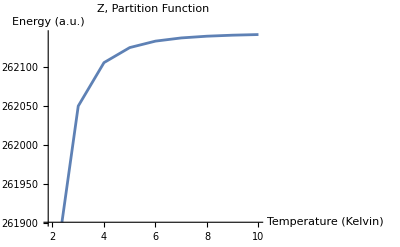

```mathematica
ListPlot[ZT, Joined->True, AxesLabel->{"Temperature (Kelvin)", "Energy (a.u.)"}, PlotLabel->"Z, Partition Function"]
```

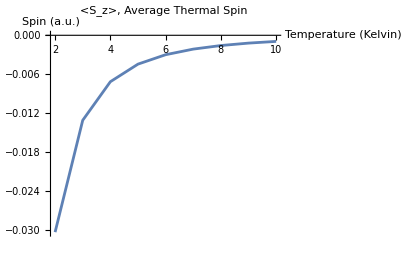

```mathematica
P1 =ListPlot[OzT, Joined->True, AxesLabel->{"Temperature (Kelvin)", "Spin (a.u.)"}, PlotLabel->"<S_z>, Average Thermal Spin"]
```

## Dispersion relations and low relaxation of spin waves in thin magnetic films

## Constants

```mathematica
(*Plank's constant*)
ℏ =6.582119569*10^-16 ;(*eV sec*) 
ℏSI = 1.054571817 10^-34;(*Joules seconds*)
(*Bohr magneton*)
μb=5.7883818060 10^-5; (*eV per Tesla*)
μbSI = 9.2740100657 10^-24;(*Joules per Tesla*)
(*Vacuum permeability*)
μ0 = 1.256637 10^-6; (*Newton per Ampere squared*)
(*Spin*)
S=1/2;
(*Lande factor*)
g=2; (*from google*)
(*The gyromagnetic ratio*)
γ = g μb /ℏ;
γSI = g μbSI /ℏ;
(*Inverse temperature*)
k=8.617333262 10^-5;(*eV per Kelvin*)(*Boltzman constant*)
T=100;(*Kelvin*)(*Temperature*)
β= 1/(k T);
(*Lattice distance*)
a=3.508 10^-10;(*meters*)(*Ref:"CrSBr: an air-stable, two-dimensional magnetic semiconductor"*)
Sa =a^2; (*See Equation (17)*)
(*Distance between layers*)
d=7.959 10^-10;(*meters*)(*Ref:"CrSBr: an air-stable, two-dimensional magnetic semiconductor"*)
(*Inter-layer coupling, i.e. coupling in the same layer.*)
I0=- 3.38 10^-3; (*eV*)(*Ref: "Spin Waves and Magnetic Exchange Hamiltonian for CrSBr"*)
(*Intra-layer coupling, i.e. coupling between diferent layers.*)
Id =0.05 10^-3; (*eV*)
(*External magetic field*)
H=0.01;(*Tesla*)
(*z-Spin, Thermal Average*)
SzAvg = -0.003;(*arbitrary units*)
(*We obtain this quantity from QFT computation in the previous computation block "Correlation for 3x3x2 lattice".*)
```

### Scaling

```mathematica
(*magnetic energy*)
{ g μbSI, (g μbSI)/(g μbSI)}
(*spin-spin exchange, same layer*)
{I0 (1.602176 10^-19), I0 (1.602176 10^-19)/(g μbSI) }
(*spin-spin exchange, different layer*)
{Id(1.602176 10^-19), Id(1.602176 10^-19)/(g μbSI)}
(*Dipole energy*)
{(μ0 (g μbSI)^2)/a^3, (μ0 (g μbSI)^2)/(a^3(g μbSI))}
(*lattice spacing: in layer, out of layer*)
{a, d, a/a, d/a}
(*Boltzman weight*)
{1/k,  (g μb)/(k)}
```

{1.8548×10^-23,1.}

{-5.41535×10^-22,-29.1964}

{8.01088×10^-24,0.431899}

{1.00144×10^-23,0.539919}

{3.508×10^-10,7.959×10^-10,1.,2.26881}

{11604.5,1.34343}

## Spin waves in magnetic bilayer

## Demagnetization Fields

```mathematica
Dstrength = NSum[4/((x^2+y^2)^(3/2)), {x, 0,∞}, {y, 1, ∞}]+ NSum[(1 -3 (d/a)^2)/(((d/a)^2 + x^2 + y^2)^(3/2)), {x, -∞, ∞}, {y, -∞, ∞}]
(*Multiplicative factor for the dipole interactions for two parallel infinite 2D lattices*)
```

NSum::nsnum: Summand (or its derivative) -(12. x √(x^2+y^2))/(((x^2+y^2)^1.5)^2) is not numerical at point y = 1..

NSum::nsnum: Summand (or its derivative) -(3. (1.-1. (3. 5.14752)) x √(5.14752+x^2+y^2))/(((5.14752+x^2+y^2)^1.5)^2) is not numerical at point y = 0.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

-30.9633

```mathematica
Dstrength= NSum[4/((x^2+y^2)^(3/2)), {x, 0,1}, {y, 1, 1}]+ NSum[(1 -3 (d/a)^2)/(((d/a)^2 + x^2 + y^2)^(3/2)), {x, -1, 1}, {y, -1, 1}]
(*Multiplicative factor for the dipole interactions for two parallel 3x3 2D lattices*)
```

-2.6358

```mathematica
(*He is the exchange field given by Equation (10)*)
He = ((4I0 + Id)/(g μb))SzAvg
(*Hm is the depolarizing magnetic field given by Equation (10)*)
Hm =((4π g μbSI μ0 Dstrength)/a^3)SzAvg
```

0.349061

0.0536503

## Normal magnetized films

```mathematica
S=1/2;
(*Hc is the self-consistent field*)
Hc = Hm + He;
(*Brillouin function Subscript[B, S][p] and B[p] = S Subscript[B, S][S p]*)
B[p_]:= (S +1/2)Coth[(S +1/2)p] - 1/2 Coth[p/2];
p = β g μb Abs[H + Hc];
(*σm is the surface magnetic moment density*)
σm= g μb B[p]/Sa;
q = √(qx^2 + qy^2);
(*Equation (21)*)
Ω[qx_, qy_, qz_]:= γ (H + Hm) + (2 B[p] I0)/ℏ(2 - Cos[qx a] - Cos[qy a])
```

```mathematica
(*Dispersion relation given by Equation (23)*)
(*Ref:"Dispersion relations and low relaxation of spin waves in thin magnetic films"*)
ω1[qx_, qy_, qz_] := (Ω[qx, qy, qz](Ω[qx, qy, qz] + 2π ((g^2 μbSI^2 B[p]μ0)/(Sa ℏSI) ) √(qx^2+qy^2)(1 + Exp[- √(qx^2+qy^2) d])))^(1/2)
ω2[qx_, qy_, qz_] := ((Ω[qx, qy, qz] + (2 B[p] Id)/ℏ)(Ω[qx, qy, qz]+ (2 B[p] Id)/ℏ + 2π ((g^2 μbSI^2 B[p]μ0)/(Sa ℏSI))√(qx^2+qy^2)(1 - Exp[- √(qx^2+qy^2) d])))^(1/2)
```

```mathematica
Ω[0, 0, 0]/10^9
ω1[0,0, 10]/10^9
ω2[10^3,-10^3, 10]/10^9
```

11.1949

11.1949

11.4055

```mathematica
WNscale=1/a;(*Wave number scaling, 1/lattice spacing*)
Fscale=10^9;(*Frequency scaling, GHz*)
Plot3D[{ω1[qx WNscale,qy WNscale, 0]/Fscale, ω2[qx WNscale,qy WNscale, 0]/Fscale}, {qx, -4, 4}, {qy, -4 , 4 }, PlotRange->Full, AxesLabel->{Text[Style["k_x/a", Bold, Black, 14]], Text[Style["k_y/a", Bold, Black, 14]], Text[Style["ω (GHz)", Bold, Black, 14]]}, PlotLabel->Text[Style["Dispersion Relation", Bold, Black, 14]]]
Plot3D[{ω1[qx WNscale,qy WNscale, 0]/Fscale, ω2[qx WNscale,qy WNscale, 0]/Fscale}, {qx, -4/2, 4/2}, {qy, -4/2 , 4/2 }, PlotRange->Full, AxesLabel->{"k_x (1/a)", "k_y, (1/a)", "ω (GHz)"}, PlotLabel->Text[Style["Dispersion Relation", Bold, Black, 14]]]
```

-Graphics3D-

-Graphics3D-

## Comparing QFT and exact computations

We check that the QFT computations give us the right computations. We perform the QFT computations and the exact computations and compare. 

The input of the QFT computations is a lattice Λ, an interaction tensor V, and an external magnetic field h. These inputs encode the Hamiltonian of the system

H = -(2 Σ_(v∈Λ) h(v)· S(v) +Σ_(v,w ∈Λ)S(v)·V(v, w)·S(w)) 

In particular,  we have

S(v) = (S_+(v), S_-(v), S_z(v)) with S_±(v) = S_x(v) ± i S_y(v)

and 

V(v,w) = (V_(i,j)(v,w))_(i, j = +, -, z)

We compare with the Hamiltonian for the XXX spin-1/2 chain. We take the lattice

Λ = {1, 2, …, λ}
H =- Σ_(k=1, ..., λ)2 h(k)· S(k) -J Σ_(k=1, ..., λ-1)S(k)·S(k+1) 

The corresponding interaction tensor in this case is 

V(k, k±1) = (0 | J/4 | 0
J/4 | 0 | 0
0 | 0 | J/2) and V(k, j) = 0 for j≠k±1

The QFT computations give a series approximation of the Quantum statistics partition function and correlation functions

Z[β] = Tr[e^(-β H)]
⟨S(v)⟩ = Tr[S(v)e^(-β H)]

where β= 1/(k T).

## Example: L=2 XXZ line

## QFT computations

### Lattice

```mathematica
L=2;
Λ = Table[{i, 0, 0}, {i, 1, L}];
λ = Length[Λ];
ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]
```

-Graphics3D-

### External Magnetic Field

```mathematica
hm=0;
hp=0;
hz=0.01;
HbExp[β_]:={{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}};
```

### Interaction Tensors

#### Constants

```mathematica
a=1;
b=1;
c=1;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
Ja=1;
Jb=1;
Jc=1;
Ds =1;
βscaling = 1;
```

#### Spin-Spin exchange Interaction

```mathematica
V[v1_,v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
r = Norm[(v1-v2)];
If[r!=1,Return[0] ];
dx= Norm[(v1-v2)[[1]]];
If[dx==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Ja/4], If[s1==3&&s2==3, Return[Ja/2]]]];
dy= Norm[(v1-v2)[[2]]];
If[dy==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jb/4], If[s1==3&&s2==3, Return[Jb/2]]]];
dz= Norm[(v1-v2)[[3]]];
If[dz==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jc/4], If[s1==3&&s2==3, Return[Jc/2]]]];
Return[0];
]
```

```mathematica
Table[V[Λ[[1]], Λ[[2]],s1, s2], {s1, 1, 3}, {s2, 1, 3}]//MatrixForm
```

(0 | Ja/4 | 0
Ja/4 | 0 | 0
0 | 0 | Ja/2)

### Correlation Function: Sz

```mathematica
acc = 2;
vIndex= 1;
sIndex=3;(*3->Subscript[S, z] spin operator*)
t=0;(*One-point correlations are independent of time b/c traces of linear operators are invariant under cyclic permutation of operators.*)
Tmin=2;
Tmax = 10;
Tdelta=1;
```

```mathematica
ZT = Table[{T, Z[acc,βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
```

```mathematica
OzTun = Table[OnePoint[acc,βscaling/T, vIndex, sIndex, t], {T, Tmin, Tmax, Tdelta}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

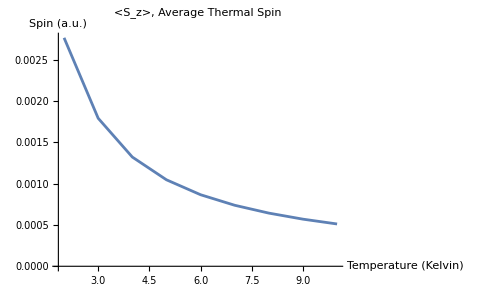

```mathematica
P1 =ListPlot[OzT, Joined->True, AxesLabel->{"Temperature (Kelvin)", "Spin (a.u.)"}, PlotLabel->"<S_z>, Average Thermal Spin"]
```

## Exact Computations

### Local Hamiltonians

```mathematica
h = (Ja/2)(KroneckerProduct[Sp, Sm] + KroneckerProduct[Sm, Sp]) + Ja (KroneckerProduct[Sz, Sz]);
Sz = {{1/2, 0}, {0 ,-1/2}};
```

### Hamiltonian

```mathematica
H =  -(Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h,IdentityMatrix[2^(λ-k-1)] ], {k, 1, λ-1}] + 2 Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sz, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]);
```

```mathematica
MatrixForm[H]
```

(-0.02-Ja/4 | 0. | 0. | 0.
0. | 0.+Ja/4 | 0.-Ja/2 | 0.
0. | 0.-Ja/2 | 0.+Ja/4 | 0.
0. | 0. | 0. | 0.02-Ja/4)

### Expected Values

```mathematica
Zexact[β_]:= Tr[MatrixExp[  -β H]];
Sz1 =KroneckerProduct[Sz, IdentityMatrix[2]];
OzExactUn[β_] := Tr[Sz1.MatrixExp[- β H]];
```

### Plots

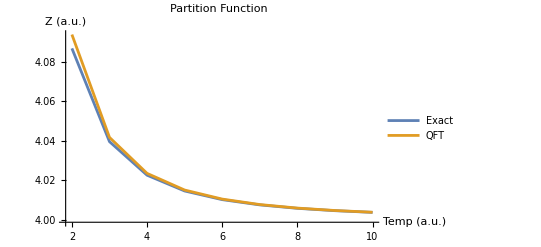

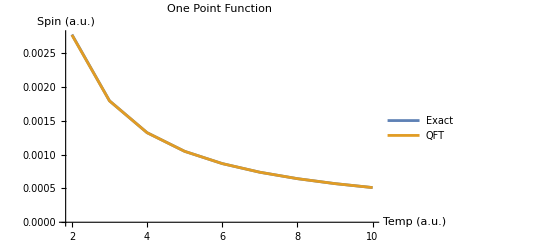

```mathematica
ZexactT = Table[{T, Zexact[βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
OzExactUnT = Table[OzExactUn[βscaling/T], {T, Tmin, Tmax, Tdelta}];
OzExactT = Table[{ZexactT[[k]][[1]], OzExactUnT[[k]]/(ZexactT[[k]][[2]])}, {k, 1, Length[ZexactT]}];
ListPlot[{ZexactT, ZT}, PlotLegends->{"Exact", "QFT"}, Joined->True, PlotLabel->"Partition Function", AxesLabel->{"Temp (a.u.)", "Z (a.u.)"}]
ListPlot[{OzExactT, OzT}, PlotLegends->{"Exact", "QFT"}, Joined->True, PlotLabel->"One Point Function", AxesLabel->{"Temp (a.u.)", "Spin (a.u.)"}]
```

## Example: L=3 XXZ line

## QFT computations

### Lattice

```mathematica
L=3;
Λ = Table[{i, 0, 0}, {i, 1, L}];
λ = Length[Λ];
ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]
```

-Graphics3D-

### External Magnetic Field

```mathematica
hm=0;
hp=0;
hz=0.01;
HbExp[β_]:={{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}};
```

### Interaction Tensors

#### Constants

```mathematica
a=1;
b=1;
c=1;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
Ja=1;
Jb=1;
Jc=1;
Ds =1;
βscaling = 1;
```

#### Spin-Spin exchange Interaction

```mathematica
V[v1_,v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
r = Norm[(v1-v2)];
If[r!=1,Return[0] ];
dx= Norm[(v1-v2)[[1]]];
If[dx==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Ja/4], If[s1==3&&s2==3, Return[Ja/2]]]];
dy= Norm[(v1-v2)[[2]]];
If[dy==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jb/4], If[s1==3&&s2==3, Return[Jb/2]]]];
dz= Norm[(v1-v2)[[3]]];
If[dz==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jc/4], If[s1==3&&s2==3, Return[Jc/2]]]];
Return[0];
]
```

### Correlation Function: Sz

```mathematica
acc = 2;
vIndex= 1;
sIndex=3;(*3->Subscript[S, z] spin operator*)
t=0;(*One-point correlations are independent of time b/c traces of linear operators are invariant under cyclic permutation of operators.*)
Tmin=2;
Tmax = 10;
Tdelta=1;
```

```mathematica
ZT = Table[{T, Z[acc,βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
```

```mathematica
OzTun = Table[OnePoint[acc,βscaling/T, vIndex, sIndex, t], {T, Tmin, Tmax, Tdelta}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

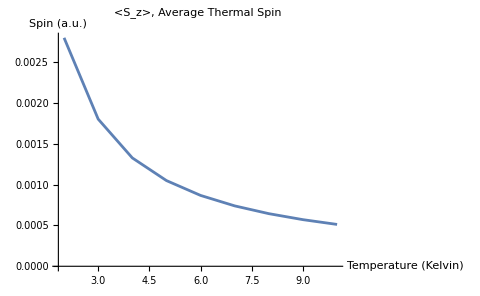

```mathematica
P1 =ListPlot[OzT, Joined->True, AxesLabel->{"Temperature (Kelvin)", "Spin (a.u.)"}, PlotLabel->"<S_z>, Average Thermal Spin"]
```

## Exact Computations

### Local Hamiltonians

```mathematica
h = ((Ja/2)(KroneckerProduct[Sp, Sm] + KroneckerProduct[Sm, Sp]) + Ja(KroneckerProduct[Sz, Sz]));
Sz = {{1/2, 0}, {0 ,-1/2}};
```

### Hamiltonian

```mathematica
H = -(Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h,IdentityMatrix[2^(λ-k-1)] ], {k, 1, λ-1}] + 2 Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sz, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]);
```

### Expected Values

```mathematica
Zexact[β_]:= Tr[MatrixExp[ -β H]];
Sz1 =KroneckerProduct[Sz, IdentityMatrix[2^(λ-1)]];
OzExactUn[β_] := Tr[Sz1.MatrixExp[-β H]];
```

### Plots

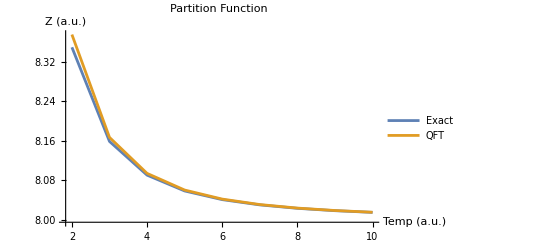

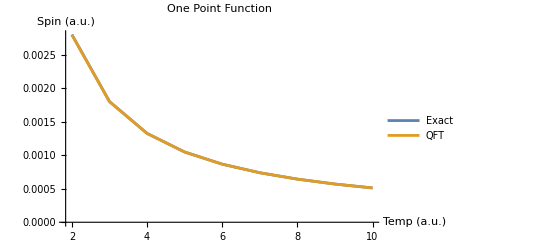

```mathematica
ZexactT = Table[{T, Zexact[βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
OzExactUnT = Table[OzExactUn[βscaling/T], {T, Tmin, Tmax, Tdelta}];
OzExactT = Table[{ZexactT[[k]][[1]], OzExactUnT[[k]]/(ZexactT[[k]][[2]])}, {k, 1, Length[ZexactT]}];
ListPlot[{ZexactT, ZT}, PlotLegends->{"Exact", "QFT"}, Joined->True, PlotLabel->"Partition Function", AxesLabel->{"Temp (a.u.)", "Z (a.u.)"}]
ListPlot[{OzExactT, OzT}, PlotLegends->{"Exact", "QFT"}, Joined->True, PlotLabel->"One Point Function", AxesLabel->{"Temp (a.u.)", "Spin (a.u.)"}]
```

## Example: L=4 XXZ line

## QFT computations

### Lattice

```mathematica
L=4;
Λ = Table[{i, 0, 0}, {i, 1, L}];
λ = Length[Λ];
ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]
```

-Graphics3D-

### External Magnetic Field

```mathematica
hm=0;
hp=0;
hz=0.01;
HbExp[β_]:={{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}};
```

### Interaction Tensors

#### Constants

```mathematica
a=1;
b=1;
c=1;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
Ja=1;
Jb=1;
Jc=1;
Ds =1;
βscaling = 1;
```

#### Spin-Spin exchange Interaction

```mathematica
V[v1_,v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
r = Norm[(v1-v2)];
If[r!=1,Return[0] ];
dx= Norm[(v1-v2)[[1]]];
If[dx==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Ja/4], If[s1==3&&s2==3, Return[Ja/2]]]];
dy= Norm[(v1-v2)[[2]]];
If[dy==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jb/4], If[s1==3&&s2==3, Return[Jb/2]]]];
dz= Norm[(v1-v2)[[3]]];
If[dz==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jc/4], If[s1==3&&s2==3, Return[Jc/2]]]];
Return[0];
]
```

### Correlation Function: Sz

```mathematica
acc = 2;
vIndex= 2;
sIndex=3;(*3->Subscript[S, z] spin operator*)
t=0;(*One-point correlations are independent of time b/c traces of linear operators are invariant under cyclic permutation of operators.*)
Tmin=2;
Tmax = 10;
Tdelta=1;
```

```mathematica
ZT = Table[{T, Z[acc,βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
```

```mathematica
OzTun = Table[OnePoint[acc,βscaling/T, vIndex, sIndex, t], {T, Tmin, Tmax, Tdelta}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

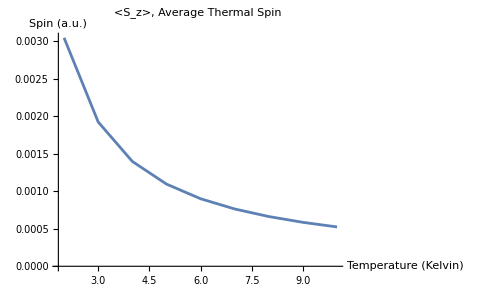

```mathematica
ListPlot[OzT, Joined->True, AxesLabel->{"Temperature (Kelvin)", "Spin (a.u.)"}, PlotLabel->"<S_z>, Average Thermal Spin"]
```

## Exact Computations

### Local Hamiltonians

```mathematica
h = ((Ja/2)(KroneckerProduct[Sp, Sm] + KroneckerProduct[Sm, Sp]) + Ja(KroneckerProduct[Sz, Sz]));
Sz = {{1/2, 0}, {0 ,-1/2}};
```

### Hamiltonian

```mathematica
H = -(Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h,IdentityMatrix[2^(λ-k-1)] ], {k, 1, λ-1}] + 2 Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sz, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]);
```

### Expected Values

```mathematica
Zexact[β_]:= Tr[MatrixExp[ -β H]];
Sz1 =KroneckerProduct[Sz, IdentityMatrix[2^(λ-1)]];
OzExactUn[β_] := Tr[Sz1.MatrixExp[-β H]];
```

### Plots

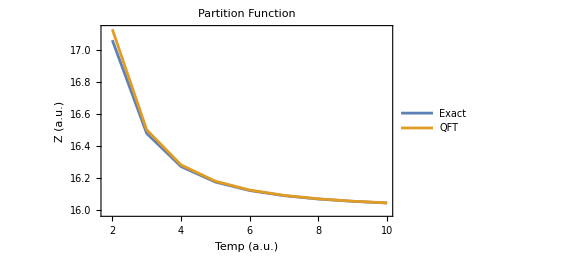

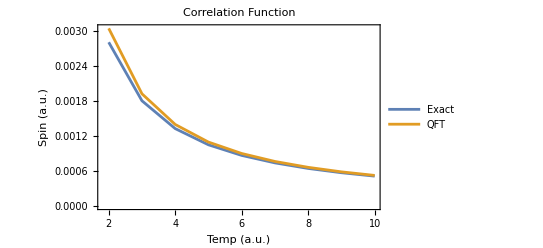

```mathematica
ZexactT = Table[{T, Zexact[βscaling/T]}, {T,Tmin , Tmax, Tdelta}];
OzExactUnT = Table[OzExactUn[βscaling/T], {T, Tmin, Tmax, Tdelta}];
OzExactT = Table[{ZexactT[[k]][[1]], OzExactUnT[[k]]/(ZexactT[[k]][[2]])}, {k, 1, Length[ZexactT]}];
ListPlot[{ZexactT, ZT}, Frame->True, PlotLegends->{Text[Style["Exact", Bold, Black, 14]], Text[Style["QFT", Bold, Black, 14]]}, Joined->True, PlotLabel->Text[Style["Partition Function", Bold, Black, 14]], FrameLabel->{Text[Style["Temp (a.u.)", Bold, Black, 14]], Text[Style["Z (a.u.)", Bold, Black, 14]]}]
ListPlot[{OzExactT, OzT}, Frame->True, PlotLegends->{Text[Style["Exact", Bold, Black, 14]], Text[Style["QFT", Bold, Black, 14]]}, Joined->True, PlotLabel->Text[Style["Correlation Function", Bold, Black, 14]], FrameLabel->{Text[Style["Temp (a.u.)", Bold, Black, 14]], Text[Style["Spin (a.u.)", Bold, Black, 14]]}]
```

## Comparing DRG with Exact computations

## Example: L=4 XXZ line

We consider a 1D spin chain with L sites.

## Exact Computations

```mathematica
λ = 4;
hz=-0.02;
hx= 0;
hy= 0;
Ja=1;
```

### Spin-1/2 Operators

We define the spin-1/2 operators where 
S_x = 1/2(0 | 1
1 | 0), S_y = 1/2(0 | -I
I | 0), S_z = 1/2(1 | 0
0 | -1)
and
S_+ = S_x + I S_y = (0 | 1
0 | 0), S_- =S_x -I S_y =(0 | 0
1 | 0).

```mathematica
Sp = {{0,0},{1, 0}};
Sm= {{0,1}, {0,0}};
Sz = {{1/2, 0}, {0 ,-1/2}};
Sx = {{0, 1/2}, {1/2 ,0}};
Sy = {{0, -I}, {I ,0}};
Ops ={Sp, Sm, Sz, IdentityMatrix[2]};
```

### Local Hamiltonian

```mathematica
h = ((Ja/2)(KroneckerProduct[Sp, Sm] + KroneckerProduct[Sm, Sp]) + Ja(KroneckerProduct[Sz, Sz]));
```

### Hamiltonian

```mathematica
H = -Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h,IdentityMatrix[2^(λ-k-1)] ], {k, 1, λ-1}] +Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sz, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hx Sx, IdentityMatrix[2^(λ-k)]], {k, 1, λ}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hz Sy, IdentityMatrix[2^(λ-k)]], {k, 1, λ}];
```

### Eigenvalues

```mathematica
Evals =Sort[N[Eigensystem[H][[1]]]]
```

{-0.839443,-0.794721,-0.75,-0.705279,-0.660557,-0.501828,-0.457107,-0.412385,-0.116025,0.205279,0.25,0.294721,0.912385,0.957107,1.00183,1.61603}

### Partition Function

```mathematica
Zexact[β_] := Sum[Exp[-β Evals[[k]]], {k, 1, Length[Evals]}]
```

### Correlation function

```mathematica
Sz1 = KroneckerProduct[IdentityMatrix[2],Sz, IdentityMatrix[2^(λ-2)]];
```

```mathematica
ESz1[β_]:= Tr[Sz1.MatrixExp[- β H]]/ Zexact[β];
```

```mathematica
Sort[Table[{Eigensystem[H][[1]][[k]], ConjugateTranspose[Eigensystem[H][[2]][[k]]].Sz1.Eigensystem[H][[2]][[k]]/Norm[Eigensystem[H][[2]][[k]]]^2}, {k, 1, 16}]]//N
```

{{-0.839443,0.223607+0. ⅈ},{-0.794721,0.111803+0. ⅈ},{-0.75,-8.74301×10^-16+0. ⅈ},{-0.705279,-0.111803+0. ⅈ},{-0.660557,-0.223607+0. ⅈ},{-0.501828,0.19086+0. ⅈ},{-0.457107,1.36002×10^-15+0. ⅈ},{-0.412385,-0.19086+0. ⅈ},{-0.116025,3.33067×10^-16+0. ⅈ},{0.205279,0.111803+0. ⅈ},{0.25,2.498×10^-16+0. ⅈ},{0.294721,-0.111803+0. ⅈ},{0.912385,0.0327465+0. ⅈ},{0.957107,2.03657×10^-15+0. ⅈ},{1.00183,-0.0327465+0. ⅈ},{1.61603,-4.85723×10^-17+0. ⅈ}}

## DMRG

### Eigenvalues

```mathematica
EvalsDMRG = {-0.789999999999998,-0.7843304055971139,-0.7516270709865368,-0.7305694084876648,-0.71388821912133,-0.5671646938259722,-0.464543538652116,-0.447588311089416,-0.11635448626225058,0.011099735780816584,0.23791699845966965};
```

### Partition Function

```mathematica
Zdmrg[β_] := Sum[Exp[-β EvalsDMRG[[k]]], {k, 1, Length[EvalsDMRG]}]
```

### Correlation Function

```mathematica
Sz1DMRG={0.49999999999997385,0.4314327174396475,0.022066255129364082,-0.24461424323958045,-0.44205559502745095,0.14289853674971467,0.15243871970344428,-0.21602017234466392,0.005253548705354975,-0.057512908025683686,0.14905220411765358};
```

```mathematica
ESz1DMRG[β_]:= Sum[Sz1DMRG[[k]]Exp[-β EvalsDMRG[[k]]], {k, 1, Length[EvalsDMRG]}]/Zdmrg[β]
```

## Comparison

### Partition Function

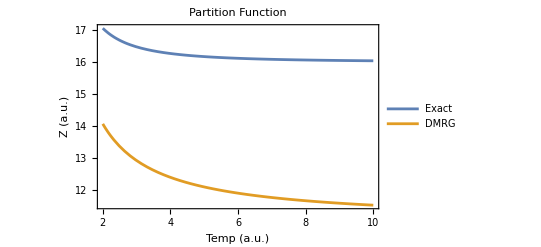

```mathematica
Plot[{Zexact[1/T], Zdmrg[1/T]}, {T, 2, 10},  Frame->True, PlotLegends->{Text[Style["Exact", Bold, Black, 14]], Text[Style["DMRG", Bold, Black, 14]]}, PlotLabel->Text[Style["Partition Function", Bold, Black, 14]], FrameLabel->{Text[Style["Temp (a.u.)", Bold, Black, 14]], Text[Style[" Z (a.u.)", Bold, Black, 14]]}]
```

Partition function don’t match because of the dimensional reduction in DMRG.

### Correlation Function

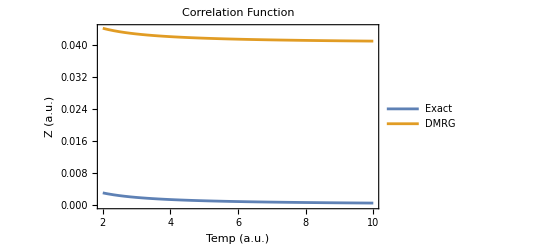

```mathematica
Plot[{ESz1[1/T],ESz1DMRG[1/T]}, {T, 2, 10}, Frame->True, PlotLegends->{Text[Style["Exact", Bold, Black, 14]], Text[Style["DMRG", Bold, Black, 14]]}, PlotLabel->Text[Style["Correlation Function", Bold, Black, 14]], FrameLabel->{Text[Style["Temp (a.u.)", Bold, Black, 14]], Text[Style[" Z (a.u.)", Bold, Black, 14]]}]
```